Note: In this problem set, expressions in green cells match corresponding expressions in the text answers.

```mathematica
Clear["Global`*"]
```

1.  Suppose a machine for filling cans with lubricating oil is set so that it will generate fillings which form a normal population with mean 1 gal and standard deviation 0.02 gal. Set up a control chart of the type shown in figure 537 for controlling the mean, that is, find LCL and UCL, assuming that the sample size is 4.

For reference, I first have to give a rendition of figure 537, using the s column.

```mathematica
slist={0.014, 0.011, 0.026, 0.023, 0.018, 0.014, 0.023, 0.017, 0.032, 0.038, 0.014, 0.011};
```

```mathematica
domlist=Range[12];
```

```mathematica
sdom=Table[{domlist[[n]],slist[[n]]},{n,12}];
```

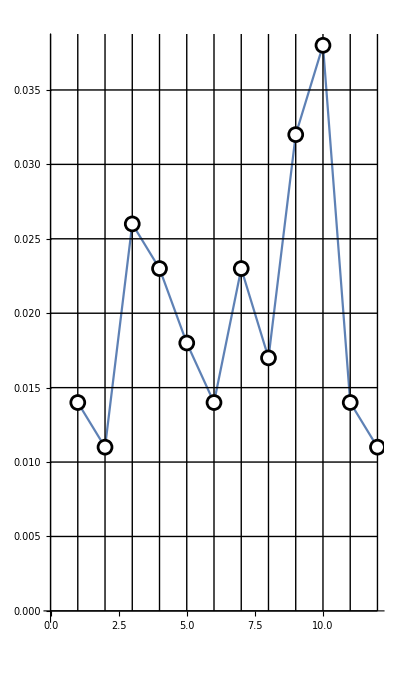

```mathematica
ListLinePlot[sdom,AspectRatio->1.7,Epilog->{{Table[Line[{{n,0},{n,0.04}}],{n,0,12}]},{Table[Line[{{0,n},{12,n}}],{n,0,0.04,0.005}]},{PointSize[0.03],Point[sdom]},{PointSize[0.02],White,Point[sdom]}}]
```

```mathematica
gv=RandomVariate[NormalDistribution[1,0.02],4]
```

{1.00253,1.00728,1.01268,0.987587}

```mathematica
dlist=Range[4];
```

```mathematica
dom2=Table[{dlist[[n]],gv[[n]]},{n,4}]
```

{{1,1.00253},{2,1.00728},{3,1.01268},{4,0.987587}}

The LCL and LCU are calculated below the plot.

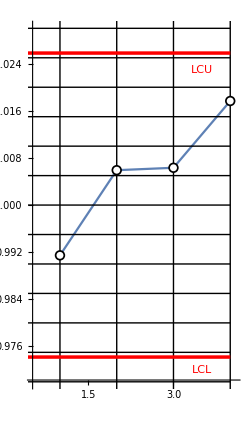

```mathematica
ListLinePlot[dom2,AspectRatio->1.7,ImageSize->250,Epilog->{{Table[Line[{{n,0},{n,1.04}}],{n,0,4}]},{Table[Line[{{0,n},{4,n}}],{n,0,1.04,0.005}]},{PointSize[0.03],Point[dom2]},{PointSize[0.02],White,Point[dom2]},{Red,Thickness[0.01],Line[{{0,1.0258},{4,1.0258}}]},{Red,Thickness[0.01],Line[{{0,0.9742},{4,0.9742}}]},{Text[Style["LCL",Medium,Red],{3.5,0.972}]},{Text[Style["LCU",Medium,Red],{3.5,1.023}]}},ImagePadding->25,PlotRange->{{0.5,4.1},{0.97,1.03}}]
```

Using numbered line (1) on p. 1089, μ_0-2.58 σ/(√n)=LCL, I can write for lower control level and upper control level,

```mathematica
elcl[a_,b_,c_]=a-2.58 b/(√c)
```

a-(2.58 b)/(√c)

```mathematica
elcu[a_,b_,c_]=a+2.58 b/(√c)
```

a+(2.58 b)/(√c)

```mathematica
elcl[1,0.02,4]
```

0.9742

```mathematica
elcu[1,0.02,4]
```

1.0258

3.  What sample size should we choose in problem 1 if we want LCL and UCL somewhat closer together, say, UCL-LCL = 0.02, without changing the significance level?

```mathematica
Solve[elcu[1,0.02,n]-elcl[1,0.02,n]==0.02,n]
```

{{n→26.6256}}

Or round up to n = 27.

5.  How should we change the sample size in controlling the mean of a normal population if we want UCL - LCL to decrease to half its original value?

```mathematica
Solve[elcu[1,0.02,n]-elcl[1,0.02,n]==0.01,n]
```

{{n→106.502}}

Increase the sample size by 2^2 .

9.  Eight samples of size 2 were taken from a lot of screws. The values (length in inches) are
Sample no. | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8
Length | 3.50 | 3.51 | 3.49 | 3.52 | 3.53 | 3.49 | 3.48 | 3.52
□ | 3.51 | 3.48 | 3.50 | 3.50 | 3.49 | 3.50 | 3.47 | 3.49
Assuming that the population is normal with mean 3.500 and variance 0.0004 and using (1), set up a control chart for the mean and graph the sample means on the chart.

```mathematica
n9={3.505, 3.495,3.495, 3.51, 3.51, 3.495, 3.475, 3.505}
```

{3.505,3.495,3.495,3.51,3.51,3.495,3.475,3.505}

```mathematica
dli=Range[8]
```

{1,2,3,4,5,6,7,8}

```mathematica
dom9=Table[{dli[[n]],n9[[n]]},{n,8}]
```

{{1,3.505},{2,3.495},{3,3.495},{4,3.51},{5,3.51},{6,3.495},{7,3.475},{8,3.505}}

```mathematica
elcu[3.500,√0.0004,2]
```

3.53649

```mathematica
elcl[3.500,√0.0004,2]
```

3.46351

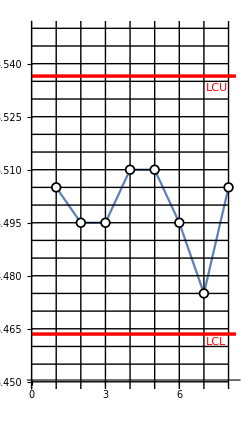

```mathematica
ListLinePlot[dom9,AspectRatio->1.7,ImageSize->250,Epilog->{{Table[Line[{{n,0},{n,8.3}}],{n,0,8}]},{Table[Line[{{0,n},{8,n}}],{n,0,4,0.005}]},{PointSize[0.03],Point[dom9]},{PointSize[0.02],White,Point[dom9]},{Red,Thickness[0.01],Line[{{0,3.53649},{8.3,3.53649}}]},{Red,Thickness[0.01],Line[{{0,3.46351},{8.3,3.46351}}]},{Text[Style["LCL",Medium,Red],{7.5,3.4614}]},{Text[Style["LCU",Medium,Red],{7.5253,3.533}]}},ImagePadding->25,PlotRange->{{0,8.3},{3.45,3.55}}]
```

11.  Number of defectives. Find formulas for the UCL, CL, and LCL (corresponding to 3 σ-limits) in the case of a control chart for the number of defectives, assuming that, in a state of statistical control, the fraction of defectives is p.

As the s.m. states, if the probability of defects is p% on each try of n tries, the number of defects forms a binomial distribution. The mean of that distribution is np, and the variance is np(1 - p). The mean will be used for the formula for CL. The problem description demands 3-σ control limits above and below CL. So

```mathematica
LCL=μ-3 σ = np-3 √(np(1-p))
```

```mathematica
LCU=μ+3 σ = np+3 √(np(1-p))
```

13.  Since the presence of a point outside control limits for the mean indicates trouble, how often would we be making the mistake of looking for nonexistent trouble if we used (a) 1-sigma limits, (b) 2-sigma limits? Assume normality.

I don’t know about nonexistent trouble, but if limits were set at 1 standard deviation, then about 30 percent of events would need to be investigated. At a setting of two standard deviations, less than 5 percent of events would need to be investigated.

```mathematica
Probability[x<-.4||x>.4,x\[Distributed]NormalDistribution[0,0.4]]//N
```

0.317311

```mathematica
Probability[x<-.8||x>.8,x\[Distributed]NormalDistribution[0,0.4]]//N
```

0.0455003

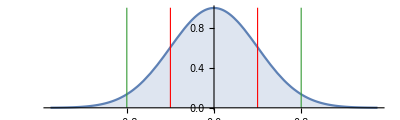

```mathematica
Plot[PDF[NormalDistribution[0,0.4],x],{x,-1.5,1.5},AspectRatio->0.3,Filling->Axis,ImageSize->400,Epilog->{{Red,Thickness[0.002],Line[{{0.4,0},{0.4,1}}]},{Red,Thickness[0.002],Line[{{-0.4,0},{-0.4,1}}]},{RGBColor[0.2,0.6,0.2],Thickness[0.002],Line[{{-0.8,0},{-0.8,1}}]},{RGBColor[0.2,0.6,0.2],Thickness[0.002],Line[{{0.8,0},{0.8,1}}]}},GridLines->All]
```

15. Number of defects per unit. A so-called c-chart or defects-per-unit chart is used for the control of the number X of defects per unit (for instance, the number of defects per 100 meters of paper, the number of missing rivets in an airplane wing, etc.). (a) Set up formulas for CL and LCL, UCL corresponding to μ ± 3 σ, assuming that X has a Poisson distribution. (b) Compute CL, LCL, and UCL in a control process of the number of imperfections in sheet glass; assume that this number is 3.6 per sheet on the average when the process is in control.

For a poisson distribution, the mean and the variance are the same. So if the mean is 3.6, the standard deviation must be

```mathematica
Clear["Global`*"]
```

```mathematica
sd=√3.6
```

1.89737

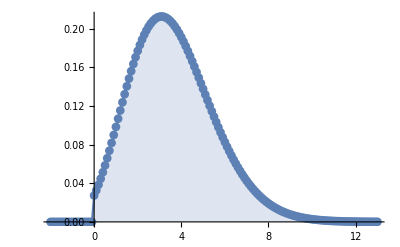

```mathematica
DiscretePlot[Evaluate@Table[PDF[PoissonDistribution[3.6],k],1],{k,-2,13,0.1},PlotRange->All,PlotMarkers->Automatic]
```

The formulas are easily set up according to the specified requirements.

The simple arithmetic gives CF=3.6, LCU=3.6 + 3(1.89737) and LCL=3.6 - 3(1.89737).